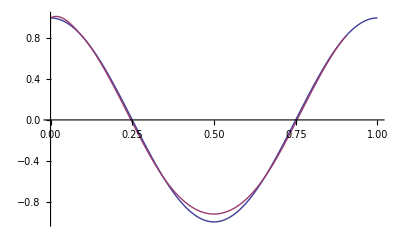

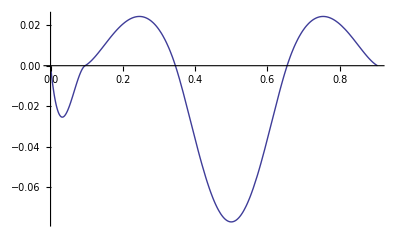

```mathematica
(* Проект по Числен Анализ 
 Илиана Красимирова Петрова,КН,гр.3,фн 80382 *)

n=5;
(*функцията,която ще бъде интерполирана от търсения естествен кубичен сплайн*)
f[t_]:= Cos[2*π*t]; 
(*генерираме интерполационните възли*)
Do[x[k]=(Sin[(k*π)/(2*n)])^2,{k,0,n}];
(*пресмятаме разстоянието между всеки два съседни възела*)
Do[h[k]=x[k+1]-x[k],{k,0,n-1}]; 
(* Решаваме система по метода на прогонката *) 
(*Изчисляваме коефициентите*)
Do[coefA[k]=1/h[k-1],{k,2,n-1}];
Do[coefB[k]=2/h[k-1]+2/h[k],{k,1,n-1}];
Do[coefC[k]=1/h[k],{k,1,n-2}];
Do[value[k]=3*(f[x[k]]-f[x[k-1]])/h[k-1]^2+3*(f[x[k+1]]-f[x[k]])/h[k]^2,{k,1,n-1}];

(*намираме алфа и бета и изразяваме съответно алфак и бетак*)
alpha[1]=-coefC[1]/coefB[1];
beta[1]=value[1]/coefB[1];
Do[alpha[k]=-coefC[k]/(coefA[k]*alpha[k-1]+coefB[k]),{k,2,n-2}];
Do[beta[k]=(value[k]-coefA[k]*beta[k-1])/(coefA[k]*alpha[k-1]+coefB[k]),{k,2,n-1}];

(*намираме d[0] i d[n] чрез втората производна на интерполиращия полином(знаем общия му вид)*)
d[0] = 3*(f[x[1]] - f[x[0]])/2*h[1] - d[1]/2;
d[n] = 3*(f[x[n]] - f[x[n-1]])/2*h[n] - d[n-1]/2;
d[n-1]=beta[n-1];

Do[d[k]=alpha[k]*d[k+1]+beta[k],{k,n-2,1,-1}];
Do[a[k]=d[k+1]/h[k]^2+d[k]/h[k]^2+2*(f[x[k]]-f[x[k+1]])/h[k]^3,{k,0,n-1}];
Do[b[k]=(f[x[k+1]]-f[x[k]])/h[k]^2-d[k]/h[k],{k,0,n-1}];
(*общ вид на полиномите интерполиращи f(t) във всеки подинтервал на [0, 1],определен от два последователни интерполационни възела *)
Do[spolinom[k,z_]=a[k]*(z-x[k])^2*(z-x[k+1])+b[k]*(z-x[k])^2+d[k]*(z-x[k])+f[x[k]],{k,0,n-1}];
(* построяване на кубичния сплайн за f(t),като вече имаме интерполуиращите полиноми за всеки един интервал (рекурсия)*)
rec[i_,t_]:=If[i≤n+1,If[t≥x[i]&&t<x[i+1],spolinom[i,t],rec[i+1,t]]];
spline[t_]:=rec[0,t];
(*изчертаваме графиките на функцията и сплайн функцията*)
Plot[{f[t],spline[t]}, {t, 0, 1}, PlotPoints->300]
(*изчертаваме графиката на разликата от функцията и сплайн функцията*)
Plot[f[t]-spline[t] , {t, 0, 1}, PlotRange->All]
```